## AutoCAD Bulge Arcs

Given an arc defined by a start point A, end point B, and a bulge factor b, find the equivalent radius r, start angle θ, and end angle ϕ.

```mathematica
BulgeToDrawArc[x_,y_,bulgeFactor_]:=Module[{ox,oy,qx,qy,b,d,r,α,β,ω,Ω},
qx=x/2;qy=y/2;d=√(qx^2+qy^2);
ω=ArcTan[x,y];Ω=ω+π/2;b=bulgeFactor/127 d;
r=(b^2+d^2)/(2b);ox=qx+(r-b)Cos[Ω];oy=qy+(r-b)Sin[Ω];
α=ArcTan[-ox,-oy];β=ArcTan[x-ox,y-oy];
If[b>0,While[α>β,α=α-2π],While[α<β,α=α+2π]];
α=α/Degree;β=β/Degree;
DrawArc[Abs[r],{α,β}]]
```

```mathematica
BulgeToDrawArc[3,3,-50]//N[#,16]&
```

DrawArc[3.111659581115951,{177.979197597198,92.02080240280199}]

```mathematica
Module[{bulgeFactor,u,d,dx,dy,px,py,ox,oy,b,r,α,β,ω,Ω},
u={1,1};
Manipulate[
dx=u⟦1⟧/2;dy=u⟦2⟧/2;d=√(dx^2+dy^2);ω=ArcTan[dx,dy];Ω=ω+π/2;b=bulgeFactor d;
r=(b^2+d^2)/(2b);β=ArcSin[(r-b)/r];
px=dx-b Cos[Ω];py=dy-b Sin[Ω];
ox=px+r Cos[Ω];oy=py+r Sin[Ω];
α=ArcTan[-ox,-oy];β=ArcTan[u⟦1⟧-ox,u⟦2⟧-oy];
If[b>0,While[α>β,α=α-2π],While[α<β,α=α+2π]];
Column[{
"α="<>ToString[N[α]],
"β="<>ToString[N[β]],
Show[Graphics[{
Line[{{0,0},u}],
PointSize[Large],
Point[{{0,0},{dx,dy},{px,py}}],
Blue,
Circle[{ox,oy},Abs[r],{α,β}],
Red,
Point[{ox,oy}]
}
],
If[Abs[dx]<Abs[dy],
Plot[dy-dx/dy(x-dx),{x,-10,10}],
ParametricPlot[{dx-dy/dx(y-dy),y},{y,-10,10}]],
PlotRange->{{-10,10},{-10,10}},
ImageSize->Large]}],
{{bulgeFactor,.1,"BF"},-1,1},
{{u,{8,8}},Locator}
]]
```

```mathematica
AutoCAD`Drawing=True
```

True

```mathematica
AutoCAD`Scale=1
```

1

```mathematica
AutoCAD`Stack={}
```

{}

```mathematica
AutoCAD`CurrentPoint={0,0}
```

{0,0}

```mathematica
AutoCADReset[]:=(AutoCAD`Drawing=True;AutoCAD`Scale=1;AutoCAD`Stack={};AutoCAD`CurrentPoint={0,0};)
```

```mathematica
ActivateDraw[]:=(AutoCAD`Drawing=True;)
```

```mathematica
DeactivateDraw[]:=(AutoCAD`Drawing=False;)
```

```mathematica
MultiplyVectors[x_]:=(AutoCAD`Scale*=x;)
```

```mathematica
DivideVectors[x_]:=(AutoCAD`Scale/=x;)
```

```mathematica
PushLocation[]:=(AutoCAD`Stack=Join[AutoCAD`Stack,{AutoCAD`CurrentPoint}];)
```

```mathematica
PopLocation[]:=(AutoCAD`CurrentPoint=AutoCAD`Stack⟦-1⟧;AutoCAD`Stack=Drop[AutoCAD`Stack,-1];)
```

```mathematica
MoveTo[x_,y_]:=Module[{cp},
cp=AutoCAD`CurrentPoint;
AutoCAD`CurrentPoint=AutoCAD`CurrentPoint+{x,y};
If[AutoCAD`Drawing,Line[{cp,AutoCAD`CurrentPoint}]]]
```

```mathematica
OctantArc[r_,sc_]:=Module[{cp,startAngle,endAngle,center},
cp=AutoCAD`CurrentPoint;
startAngle=BitShiftRight[BitAnd[Abs[sc],16^^70],4]×π/4;
endAngle=startAngle+Sign[sc]×BitAnd[Abs[sc],16^^7]×π/4;
center=cp+{r Cos[startAngle-π],r Sin[startAngle-π]};
AutoCAD`CurrentPoint=center+{r Cos[endAngle],r Sin[endAngle]};
If[AutoCAD`Drawing,Circle[center,r,{startAngle,endAngle}]]]
```

```mathematica
FractionalArc[startOffset_,endOffset_,highRadius_,lowRadius_,sc_]:=Module[
{cp,r,startAngle,endAngle,center},
r=highRadius×256+lowRadius;
cp=AutoCAD`CurrentPoint;
startAngle=(BitShiftRight[BitAnd[Abs[sc],16^^70],4]+startOffset/256)×π/4;
endAngle=startAngle+Sign[sc]×(BitAnd[Abs[sc],16^^7]+endOffset/256)×π/4;
center=cp+{r Cos[startAngle-π],r Sin[startAngle-π]};
AutoCAD`CurrentPoint=center+{r Cos[endAngle],r Sin[endAngle]};
If[AutoCAD`Drawing,Circle[center,r,{startAngle,endAngle}]]]
```

```mathematica
BulgeArc[x_,y_,bulgeFactor_]:=Module[{ox,oy,qx,qy,b,d,r,α,β,ω,Ω},
If[bulgeFactor==0,MoveTo[x,y],(
qx=AutoCAD`CurrentPoint⟦1⟧+x/2;qy=AutoCAD`CurrentPoint⟦2⟧+y/2;d=√((x/2)^2+(y/2)^2);
ω=ArcTan[x,y];Ω=ω+π/2;b=bulgeFactor/127 d;
r=(b^2+d^2)/(2b);ox=qx+(r-b)Cos[Ω];oy=qy+(r-b)Sin[Ω];
α=ArcTan[AutoCAD`CurrentPoint⟦1⟧-ox,AutoCAD`CurrentPoint⟦2⟧-oy];
β=ArcTan[AutoCAD`CurrentPoint⟦1⟧+x-ox,AutoCAD`CurrentPoint⟦2⟧+y-oy];
If[b>0,While[α>β,α=α-2π],While[α<β,α=α+2π]];
AutoCAD`CurrentPoint=AutoCAD`CurrentPoint+{x,y};
If[AutoCAD`Drawing,Circle[{ox,oy},Abs[r],{α,β}]])]]
```

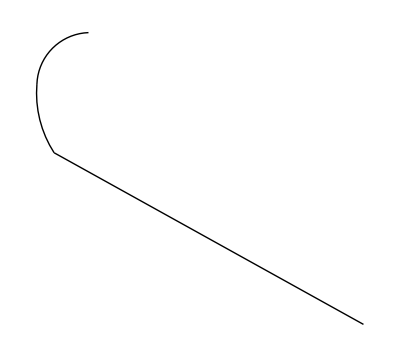

```mathematica
Graphics[{
AutoCADReset[],
DeactivateDraw[],
MoveTo[11,1],
ActivateDraw[],
MoveTo[-7,11],
BulgeArc[-1,4,-21],BulgeArc[3,3,-50]
}]
```

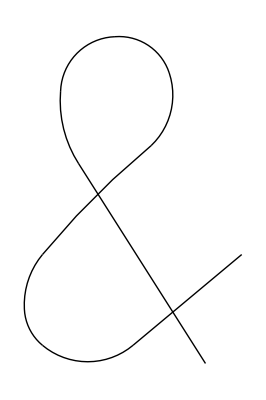

```mathematica
Graphics[{
AutoCADReset[],
DeactivateDraw[],
MoveTo[11,1],
ActivateDraw[],
MoveTo[-7,11],
BulgeArc[-1,4,-21],
BulgeArc[3,3,-50],
BulgeArc[3,-2,-44],
BulgeArc[-1,-4,-37],
BulgeArc[-6,-6,6],
BulgeArc[-1,-3,24],
BulgeArc[1,-2,27],
BulgeArc[5,0,46],
BulgeArc[6,5,0],
DeactivateDraw[],
MoveTo[5,-7]}]
```

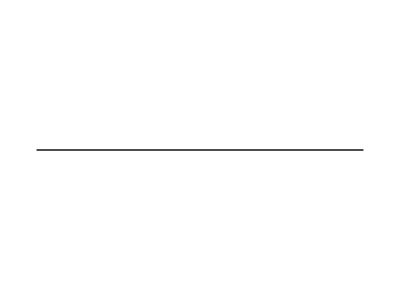

```mathematica
Graphics[{
AutoCADReset[],
DeactivateDraw[],
MoveTo[1,11],
ActivateDraw[],
MoveTo[5,0]}]
```

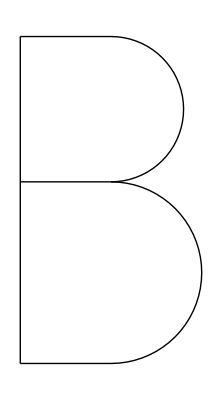

```mathematica
Graphics[{
AutoCADReset[],
DeactivateDraw[],
MoveTo[1,11],
ActivateDraw[],
MoveTo[5,0],
OctantArc[5,-(16^^24)],
MoveTo[-5,0],
MoveTo[0,18],
MoveTo[5,0],
OctantArc[4,-(16^^24)],
DeactivateDraw[],
MoveTo[10,-11]}]
```